```mathematica
ArcTan[1]
```

π/4

```mathematica
Tan[π/4]
```

1

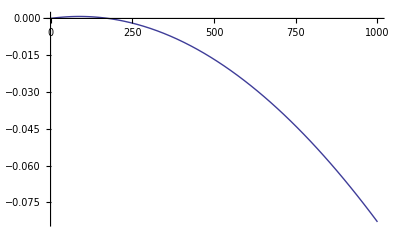

```mathematica
Clear[x,z,ω,S,λ,w,p]
q[x_,z_]:=(4π Sin[θ[x,z]])/λ
qx[x_,z_,ω_]:=(4π Sin[θ[x,z]])/λ Cos[θ[x,z]]Cos[ϕ[x,z]]
qy[x_,z_,ω_]:=(4π Sin[θ[x,z]])/λ(-Sin[θ[x,z]]Cos[ω]+Cos[θ[x,z]]Sin[ϕ[x,z]]Sin[ω])
qz[x_,z_,ω_]:=(4π Sin[θ[x,z]])/λ(Sin[θ[x,z]]Sin[ω]+Cos[θ[x,z]]Sin[ϕ[x,z]]Cos[ω])
θ[x_,z_]:=0.5 ArcTan[(p*x)/S(Cos[ArcTan[z/x]])^-1]
ϕ[x_,z_]:=ArcTan[z/x]

S=360 (*mm*);
w=1 Degree;
λ=1.18 (*Angstrom*);
p = 0.07113 (*mm per pixel*);
Plot[qy[0.00000001,z,w],{z,0.000000001,1000}]
```

```mathematica
qx[1,300,1 Degree]-qx[2,300,1 Degree]
qx[1,300,2 Degree]-qx[2,300,2Degree]
```

-0.00105024

-0.00105024

```mathematica
Sin[90]
```

Sin[90]